# Schijf LCA: Numeriek

Hier lost men het LCA probleem voor een schijf op aan de hand van NDEigensystem.

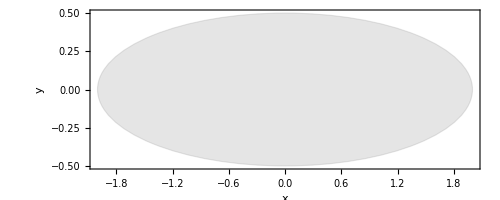

{{2.1173×10^-14,0.886641,3.01049,6.34152,10.8728,11.3536,15.2351,16.6,19.9608,23.521,25.5885,31.6329,32.1655,39.7311,40.9353,42.5945,48.3176,49.6993,51.4313,57.6278,57.9466,63.1146,66.4172,68.648,75.9949,76.1101,80.4318,86.7299,90.0864,93.3375,93.7053,98.3241,104.05,105.357,107.352},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Ω = 1/Sqrt[2Pi];
R = {2,0.5};
n = 35;

Graphics[{EdgeForm[Thin],Opacity[0.2],Gray,Disk[{0,0}, R]}, Frame->True,FrameTicks->{{{None,None},None},{{None,{R[[1]],"R"} },None}}, Axes->True, AxesLabel->{x,y}, PlotRange->Automatic]

{vals, funs} = NDEigensystem[{-Laplacian[u[x,y],{x,y}]+NeumannValue[0, {x,y} ∈ Circle[{0,0}, R]]}, u, {x,y} ∈ Disk[{0,0}, R], n]
Table[Plot3D[funs[[i]][x,y], {x,y} ∈ Disk[{0,0}, R], AxesLabel->Automatic ,PlotRange->All, PlotLabel->vals[[i]]],{i,1,n}]
```

# Schijf: Coulomb

De eigenfuncties van het probleem in LCA kunnen opnieuw gebruikt worden om het probleem met de Coulomb potentiaal in te ontwikkelen.

```mathematica
Lm = ParallelTable[Ω^2 NIntegrate[(funs[[i]][x1,y1] Conjugate[funs[[j]][x2,y2]])/(√((x1-x2)^2 + (y1-y2)^2+(0.0001)^2)), {x1,y1} ∈  Disk[{0,0}, R],{x2,y2} ∈  Disk[{0,0}, R], PrecisionGoal->6,AccuracyGoal->6,Method->{"SymbolicDomainDecomposition",Method->{"GlobalAdaptive","MaxErrorIncreases"->7000}},MinRecursion->50,MaxRecursion->130, WorkingPrecision->15],{i,1,n},{j,1,n}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.9025406079257 and 0.157302112261368 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.014298756213512 and 0.12812718235567 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000918931257865088 and 0.108309032201224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0768840009587762 and 0.118656709405229 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.17116365588286770286793039274041606342533242470772587037530946026 and 0.083654495424449912992285609860104652510427320515797829555745374943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00077102569572929636835912009881710698928907628802956985652720014852 and 0.10170099193513372074532084181509666284532705854505590910280519511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.014542540735770041111076394636220603671756971757615222690162363733 and 0.12207248583513575665955838096248009451356856543252778129803024615 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.32457178915357848869472378633084881497349586194732400656680734669 and 0.1076348518256649088597027330895936137247507331904020318048639476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000526573826940574 and 0.0865279143848994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000334273246436601 and 0.10179366277842 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.011067481519660600252280342182227803672568495675174037185529353373 and 0.04140579115818613386959031548903216654852343886107607087521793626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00045815605445790754565996145049669671848859127306450540910852730676 and 0.086349218600667305048009823351015205550847699225539840225013505372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.537375900718972 and 0.12195865017342 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.025099412848982835893096940020279365263188945857164506190015474497 and 0.10122426261908232174361544998828337300434502516096601078800153966 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001097167552808 and 0.0742154420032858 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.103729253255547 and 0.114364970083284 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.12973466089398145404138496952093347384632929466052713676409562029 and 0.066548166648024283715558724300744334774092751354782016779500767498 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00017041305389665734156843389276918315782929334722356124143245414757 and 0.090087138979412036738391899676622044318052331072720643638933223968 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0171971567876054 and 0.144004096295978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.023075866736015717574830472283344135123892847241507721216311345463 and 0.11745507824665518433530682954346521339322300787337152325166179032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0157599195697328 and 0.12844481802704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.044499488337424310511700203689418260291376001168183150221310720869 and 0.11121883141091762034492134749971411032129560705456241175939869872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0024082932964806159486878908663228336403409627391517327254249708715 and 0.11236434690282821284790489967009001280107492345609433398111200388 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.028041788283942 and 0.111408004628508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.018903067055444435617386435263410702139926403070277058602298736994 and 0.11908146839973396743980768971389557386208973049823480171010649594 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.039014129717287159794072769103289188561496300344248133321718711873 and 0.10593294779301203918269518980886835918072809847551104025129748462 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0161622794384669 and 0.108050341163425 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0117446783277861 and 0.117128126192479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.073333252119523940515656318361783251657235450358169885748981035289 and 0.08938915252148712638105088128982617727137537207047068539763577163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00165288652417395 and 0.0783297526010894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.010500571376731091285513265104898678307510619777311376737818377927 and 0.098676701219137440714682348965792648233127252251630423883432933564 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00312007537387493 and 0.030399449860365 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00106170472624395 and 0.0667587573298182 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.01394747279076846900049025695978934166586599400500548804726929038 and 0.14285852719436578992188445544565048756403254735923153096204164182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.028585355316884368694185634690513009187272386249588409545459399136 and 0.1266184299538490875966372541062932838304272481889988513582442006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 7000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.010452366369604404464607432171692979391970922735706674318329796556 and 0.1295021468823328700039767083145773089894378067250440037246568091 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{0.78026357146012,-0.00231451724321305,0.085526030897884,0.00227571773144638,-0.018845695398718,0.00333770079462794,-0.0000146252452049333,0.00283996316234451,-0.0000214247143715691,0.0122364687972715,0.0000292643942761707,-0.00303970808564006,-0.000122712550726523,0.0000274249909029255,-0.00673332714674503,-0.0272415419114386,0.000169151651015203,0.000240099590681441,0.00273701250987382,-0.0199250174494154,0.000205070318959682,0.00367263825716674,0.00263572670047167,0.000143454791355757,0.00250826910225367,-0.00923915186001842,-8.86563004076752×10^-6,-0.00186922361089141,0.00370233838626665,0.000163221868129458,0.000263065060692266,0.00801571701390487,0.000510971190043226,0.00221980923829051,0.00040321797973997},{-0.00231451724321305,0.424236575284118,0.000609451262583916,-0.0516572046319724,-0.000427258750052147,-0.000054700861309673,-8.38068274623847×10^-6,0.0210670049120773,0.0000906604576514792,0.0000532012395134324,-0.0000238156426213589,0.0110741542903004,0.0000729178007748864,0.00013651927942682,0.00101677042448621,-0.00176144439143219,-0.0000581101590984778,0.0236386470544805,0.00708231353396112,0.00102518371575166,0.000244819317007856,-0.000383291782549969,-0.0164984375996875,0.000260545420257362,-0.00446298921852577,-0.000398722133012948,-2.12155440586661×10^-6,-0.0116713495678264,-0.000588360530257457,0.0000449971886308889,0.000496575418571488,0.00280236380563221,-0.000019785866498317,0.00454950059872034,0.000262794520884009},{0.085526030897884,0.000609451262583913,0.338562783274648,0.00399469562361985,0.035913957796954,1.9307483988187×10^-6,-0.0000174619639429408,0.00372710518832316,-0.0000730663436634664,-0.0165090233988516,0.0000320741929153836,-0.00273146861053094,-0.0000271220798947774,0.0000308931277527625,0.00522798801287528,-0.020647912571628,0.0000650748311507712,0.00342427691048829,0.00300851656147147,0.00770078956432948,-0.000302083225841027,-0.00620929159493466,0.00209944198681223,0.000197461254096005,0.00257230666426451,0.00924530632801427,0.0000589522103463162,-0.00167121783989497,-0.00194117839990279,0.000094752501463228,0.000168975555285753,-0.0109732345620487,0.0000638131140497442,0.00166354577473003,0.000944058498339493},{0.00227571773144638,-0.0516572046319724,0.00399469562361985,0.268198956983521,0.000446280191797466,-5.17664362767649×10^-6,0.000077406257269446,0.0219527602207337,-0.000028461692614973,0.000571400183598216,0.000115703570236548,0.0110155038004666,-0.0000826227351350505,-0.0000497154254868152,0.0000264690309839253,0.00323198773847244,-0.00012821224711227,-0.0254570894968082,0.00653943700657359,-0.000440923279264031,-0.0000815271996609027,0.000218068806828531,0.00077342435678126,-0.0000519887172599109,-0.00412429522105167,-0.00031781223120224,-0.000140296601008405,-0.0046452134725733,0.000303337285560196,0.000241428565565607,0.0000796476905016666,0.000122285624089244,0.000136298578952809,0.00384435136597698,0.000012493057896513},{-0.018845695398718,-0.000427258750052147,0.035913957796954,0.000446280191797466,0.22926504557301,0.0000159562551812759,-0.000724476218536185,0.00307899819714967,-0.000710515927705397,0.0152603784592692,-0.000265371993598656,-0.00343820732666224,0.0000492593960022516,0.0000223414976939871,-0.0110799797394807,-0.00337086748594788,-0.000290499158298549,0.00324925142463046,0.00361313681691986,0.0209356010302695,-0.000424881480762718,0.00387298836324116,0.000936523846555042,-0.0000933213595790231,0.00232930422873956,0.00400038650166953,0.000124058688507468,-0.00215715962118601,0.00666285514119388,0.00032047046030887,0.0000555183089650821,0.000120462802235129,0.0000829413208653095,0.000287152290803275,0.000777777684265967},{0.00333770079462794,-0.0000547008613096729,1.93074839881852×10^-6,-5.17664362767649×10^-6,0.0000159562551812759,0.258988882013625,0.0103948754484196,0.00010088213188841,-0.00353530919534674,-0.0000681871079829207,0.00508801272459713,2.91783026614742×10^-6,0.00580754811780349,-0.00790385853277884,0.0000224202236539914,-1.52525691892349×10^-6,-0.00213859816025536,0.000185386725389736,0.0000739251354783165,0.0000167729345895074,0.00519259204079888,-0.0000333142237671346,0.0000490068897552082,0.00144914130279722,0.0000249599979911165,0.000147344815333372,-0.00618558093795048,-0.000436930049592927,-0.0000502650004052144,-0.0013812708608591,0.00626669256797231,-0.000280426754060837,-0.00288650203083445,0.00118254013245023,-0.00620188008654245},{-0.0000146252452050882,-8.38068274604086×10^-6,-0.0000174619639429432,0.000077406257269446,-0.000724476218536235,0.0103948754484196,0.200570300999033,1.72275642055733×10^-6,-0.00131430487627527,-0.000155230357204611,-0.000314570210421219,-0.00002554647686867,0.00217895994814087,-0.000650872640549593,-0.0000125441722975623,-0.0000611183380057444,0.0000245603912550629,0.000143641562369381,-0.0000470216201712674,0.0000664136379253329,0.000744748078415555,-0.0000966263787185374,0.000104641998492511,0.00168417947495953,0.00112130177834365,0.000139734338492179,-0.000717487593717981,0.000219396008431163,0.0000613033543336825,0.000265878749399075,-0.00506821633968038,-0.0000597003668223967,0.0166230613001059,-0.0000953601342405561,0.000255148835575516},{0.00283996316234459,0.0210670049120772,0.00372710518832316,0.0219527602207337,0.00307899819714967,0.000100882131888482,1.72275642082455×10^-6,0.195186933630929,-0.0000300281848867295,0.00140968223277646,0.0000322147210424667,-0.013480960859543,0.0000539025570331886,-0.0000534063288277543,0.157823695854343,0.0037131273449828,-0.000111699771812132,-0.00797059368469885,-0.00735043167828004,-0.0013830441191391,0.00230997047734848,-0.000220736636189261,-0.0171644291105426,0.000445045196791882,0.00629250025940895,0.000457900334129229,-0.000107516244693459,-0.00561243374334685,0.000122867707110975,-0.0000655130861404203,0.000010843583325839,-0.000305914224054318,-0.000174601179336937,-0.00420029985111585,-0.000104091377994906},{-0.0000214247143716822,0.0000906604576516236,-0.00007306634366347,-0.0000284616926149803,-0.000710515927705473,-0.00353530919534674,-0.00131430487627541,-0.0000300281848871315,0.177583757974532,0.0000246757160662768,-0.00468289487984657,-0.000150351620124621,-0.000502605650499715,0.00512728213422425,0.000146996022087764,-0.00283039751463852,0.00529369213654631,0.000286144194621178,-0.000156273780908395,0.000630086697185286,-0.00387385434689843,0.000316142530486451,-0.0000632729905174086,0.00370474829872968,-0.0000402128909529667,0.000130407526210424,0.00357548525912545,-0.00881891701965795,-0.00009278108063278,0.00503129563386406,-0.00565907528966338,0.000248876969815974,0.00281787027857905,-0.0000139059509791657,0.00260049283077217},{0.0122364687972712,0.0000532012395137603,-0.0165090233988514,0.000571400183598216,0.0152603784592692,-0.0000681871079829207,-0.000155230357204611,0.00140968223277646,0.0000246757160662768,0.171288995545318,0.000713688126377206,-0.00244432026173085,0.000136702536632371,0.000393649963807889,0.008279078501749,0.000184464990507737,0.0000976623625894922,0.000879191317632883,0.000919080295039996,0.00751164332047183,0.000249864738218775,-0.00790061603683768,0.0019384593854878,-0.000109130048649596,0.00163086102872851,-0.0148817750837795,-0.00126307408857367,-0.000538272658645309,-0.00373130810033418,-0.0000506055038554345,-0.00104872696068945,0.00309275854180228,0.000175018958284445,0.00164535998506444,-0.000292601279053443},{0.0000292643942761046,-0.0000238156426212747,0.0000320741929154347,0.000115703570236573,-0.000265371993598573,0.00508801272459713,-0.000314570210421303,0.0000322147210426411,-0.0046828948798467,0.000713688126377206,0.160283898969493,-3.96515486031174×10^-6,0.00108319274149271,-0.00257128627046249,-0.0000238204975149229,-0.000120122953419158,0.000809318773100201,-0.0000386612707413654,-0.000113663239735867,0.00013485145426408,-0.000562957235114532,0.00046171884115089,0.00019657358216449,-7.94421484468555×10^-6,-0.000225885462672919,0.0000828568732016928,-0.000742686613600712,-0.000079125054458305,0.000121482205339407,4.36139051311964×10^-6,-0.00115634178896038,-0.0000684751995614282,0.00647661559473346,0.000102795220126881,-0.00114325106423603},{-0.00303970808564006,0.0110741542903004,-0.00273146861053094,0.0110155038004666,-0.00343820732666224,2.91783026614742×10^-6,-0.00002554647686867,-0.013480960859543,-0.000150351620124621,-0.00244432026173085,-3.96515486031174×10^-6,0.154749242793426,0.000109458722253279,-0.0000719309081578497,-0.000842423514750072,-0.00397611211609202,0.000597342335386188,-0.0000549112064769362,-0.00846014530002056,0.00192082034516143,-0.000299446364107879,0.000149160921387024,0.00521565885059169,-0.0000826761790725773,0.00589600402613266,-0.000878606952829421,0.00035534658058654,-0.01027068907113,-0.00093132304875588,-0.000306122482090557,0.000133241681333461,0.000039139268566568,-0.000252219719980011,-0.00377929235371122,-0.000286411771124553},{-0.000122712550726185,0.0000729178007744556,-0.0000271220798950386,-0.0000826227351350624,0.0000492593960022516,0.00580754811780349,0.0021789599481413,0.0000539025570331886,-0.000502605650499064,0.000136702536632794,0.00108319274149199,0.000109458722253279,0.146662889915211,-0.00491669123504872,-0.0000389227474537738,-1.32233909221349×10^-6,0.00175511934763728,-0.0000861195133305962,0.0000406250272800672,-0.000623838494995915,0.0031875270113695,0.000766506262784068,-0.000151639158797783,-0.00259087965891447,-0.000029504802681943,-0.0000663479294068074,-0.00559465288780043,0.0000750942273401232,-0.00021950935455781,-0.00311731715113923,-0.00247337924511239,0.0000660422115799686,-0.00136467164796049,0.000143603076494773,-0.00372297358904675},{0.0000274249909023019,0.000136519279427615,0.0000308931277532483,-0.0000497154254867837,0.0000223414976939871,-0.00790385853277884,-0.000650872640550387,-0.0000534063288268709,0.00512728213422305,0.000393649963807016,-0.00257128627046116,-0.0000719309081578497,-0.00491669123505004,0.133179912649308,-0.000766855116367367,0.0000379795799961191,-0.00188862042784848,-0.0000166119622645986,-0.0000619178757504706,-0.000349660196290126,-0.00620473888400683,-0.0000435161475357396,0.0000201792953688882,-0.00183902618151317,-0.00130738548383251,-0.0000404402896764748,0.00106622448654771,-0.000211163801812305,0.0000397416782606944,0.00139211325232264,0.00392744796035912,-0.000143619242540726,-0.00230762765937533,-0.0003025357977352,-0.000455963793564437},{-0.00673332714674503,0.00101677042448621,0.00522798801287528,0.0000264690309839253,-0.0110799797394807,0.0000224202236539914,-0.0000125441722975623,0.157823695854343,0.000146996022087764,0.008279078501749,-0.0000238204975149229,-0.000842423514750072,-0.0000389227474537738,-0.000766855116367367,0.136473298931518,0.000194381011782477,-0.00018987245846552,0.0012626463919552,0.00228770595973937,0.00481742756236247,-0.000474249068837141,0.00456756380621645,0.0000665732973180258,0.000267717806361567,0.00182961831964191,-0.00725049730437375,-0.000178116615607385,-0.0019760324245063,0.0059712601589661,0.0000451783057238298,-0.00112486838019094,-0.0114194472585352,-0.000177088171918777,0.000498243791318397,-0.000111188730594692},{-0.0272415419114386,-0.00176144439143219,-0.020647912571628,0.00323198773847244,-0.00337086748594788,-1.52525691912101×10^-6,-0.0000611183380057444,0.0037131273449828,-0.00283039751463854,0.000184464990507737,-0.000120122953419158,-0.00397611211609202,-1.32233909219383×10^-6,0.0000379795799961191,0.000194381011782477,0.166713673266079,0.000256308944127384,0.00748237839530345,0.00320271611313207,-0.000783093095903969,0.0000430056826252115,-0.0000482889106134079,0.00420314743757234,0.000245308856184252,0.00346414322210707,0.00370820537911741,0.000106050299565352,-0.00448209884695908,-0.000560853473660693,0.0000881828558001518,-0.00011391409846195,-0.000573687841791704,-0.00015112974502646,0.00366292868176518,0.000152708368996925},{0.000169151651015203,-0.0000581101590984787,0.000065074831150774,-0.000128212247112248,-0.000290499158298549,-0.00213859816025536,0.0000245603912550629,-0.000111699771812132,0.00529369213654627,0.0000976623625894922,0.000809318773100301,0.000597342335386188,0.00175511934763707,-0.00188862042784809,-0.00018987245846552,0.000256308944127388,0.116478448241894,0.000197828772977671,-0.000409487899642216,0.00010894664549015,0.00241652320826297,-0.00017513646104018,-0.0000554296087957266,-0.00246968679174572,-0.00112954523257298,-0.000210594258016134,-0.0030393115987999,0.000142380988726181,0.000459762678267594,-0.00549514069320541,0.00210819070875606,-0.000031203162953718,-0.00169357756363845,-0.000519537541119763,-0.00152427131061728},{0.000240099590680752,0.0236386470544813,0.00342427691048829,-0.0254570894968082,0.00324925142463046,0.000185386725389736,0.000143641562369381,-0.00797059368469885,0.000286144194621178,0.000879191317632883,-0.0000386612707413654,-0.0000549112064769362,-0.0000861195133305962,-0.0000166119622645986,0.0012626463919552,0.00748237839530345,0.000197828772977671,0.133013741684882,0.00125409315529507,-0.00153280744029155,-0.0000409193774957359,0.000502957882299326,0.000683874369086075,-0.0000614378086626545,0.00159801283565279,0.000771259480680853,0.000431632251055463,-0.0024725473901908,0.0000300401733407799,-0.0000422357477914925,0.00119618548258829,-0.0000522313979890412,0.000118720455662135,0.001579885703576,-0.000464388622708222},{0.00273701250987374,0.00708231353396123,0.00300851656147154,0.00653943700657359,0.00361313681691986,0.0000739251354783165,-0.000047021620171219,-0.00735043167827993,-0.000156273780908322,0.000919080295039994,-0.000113663239735946,-0.00846014530002056,0.0000406250272801289,-0.0000619178757504706,0.00228770595973937,0.00320271611313207,-0.000409487899642216,0.00125409315529507,0.125543056881402,0.000365589834699007,0.0000354867249762488,0.000438738267860157,0.00362863903519596,0.000308111428047943,0.00524909114235229,0.00118554860867338,-0.0000758516027526748,0.00435459041154272,-0.000221903754948328,-0.000289382094329114,0.0000945596119643522,0.0000344127961614395,-0.0000293267978723454,-0.00535066084149368,0.000206465880078438},{-0.0199250174494167,0.00102518371575329,0.00770078956432948,-0.000440923279264031,0.0209356010302695,0.0000167729345895074,0.0000664136379253329,-0.0013830441191391,0.000630086697185286,0.00751164332047183,0.00013485145426408,0.00192082034516143,-0.000623838494995915,-0.000349660196289518,0.00481742756236247,-0.000783093095903969,0.00010894664549015,-0.00153280744029155,0.000365589834699007,0.12198872851846,0.0000538554894051006,0.00340171595371948,-0.00180776645703845,-0.000176504139491463,-0.00224779617427921,0.00175868379708972,-0.0000292822454559522,0.00252591396626951,-0.0028225608611213,0.000110688653252594,0.0012128549756507,0.00176972122879302,-0.000204954394238044,-0.000482306457912093,-0.000393033557129445},{0.000205070318960919,0.000244819317009367,-0.000302083225840111,-0.0000815271996609027,-0.000424881480762718,0.00519259204079888,0.000744748078414197,0.00230997047734529,-0.00387385434690275,0.000249864738217118,-0.000562957235109772,-0.000299446364107879,0.00318752701136942,-0.00620473888400668,-0.00047424906883723,0.0000430056826252115,0.00241652320826297,-0.0000409193774957359,0.0000354867249761887,0.0000538554894051006,0.11534071014638,-0.000268258876719638,0.000169233989883625,-0.000389514102027579,0.0013247717805441,0.000484910871406146,-0.00505852291248197,-0.000186435542883811,0.0000874983727875774,-0.0000586980839622774,-0.00159026075678658,-0.0000500883472003714,-0.000517050147648968,0.0000511012999198641,0.0010797623531636},{0.00367263825716674,-0.000383291782549965,-0.00620929159493466,0.000218068806828531,0.00387298836324116,-0.0000333142237667733,-0.0000966263787177164,-0.000220736636189257,0.000316142530487682,-0.00790061603683768,0.000461718841149537,0.000149160921387024,0.000766506262784068,-0.0000435161475357396,0.00456756380621645,-0.0000482889106134079,-0.00017513646104018,0.000502957882299326,0.000438738267860157,0.00340171595371948,-0.000268258876719638,0.116211101871423,-0.000256755992884696,0.000224699378010481,0.00132772564769111,-0.00272161548989955,0.000376542985580194,-0.000472939780870009,-0.00361638839833069,0.000340067130041763,0.0000100257623164372,-0.00781016125121677,-0.000335942136005344,0.0000943796062793717,0.000357974341393237},{0.00263572670047346,-0.0164984375996898,0.00209944198681085,0.000773424356781376,0.000936523846555042,0.0000490068897552082,0.000104641998494797,-0.0171644291105426,-0.0000632729905139562,0.0019384593854874,0.000196573582164387,0.00521565885059169,-0.000151639158797783,0.0000201792953679171,0.0000665732973180258,0.00420314743757234,-0.0000554296087957266,0.000683874369086075,0.00362863903519596,-0.00180776645703845,0.000169233989883625,-0.0002567559928847,0.117683235087433,0.0000904808164955297,0.00108739703335356,0.00152813146267149,-0.00024428112139173,-0.00144124195956214,-0.00158899241075469,0.00016628654305958,-0.0000920547656318382,-0.000533202926809616,0.000137838424569993,0.00146078345211248,-0.000069037213107672},{0.000143454791355757,0.000260545420257362,0.00019746125409603,-0.0000519887172597842,-0.00009332135958046,0.00144914130279722,0.00168417947495953,0.000445045196791861,0.00370474829872968,-0.00010913004865108,-7.94421484468555×10^-6,-0.0000826761790725773,-0.00259087965891447,-0.00183902618151317,0.000267717806362628,0.000245308856184322,-0.00246968679174572,-0.0000614378086626545,0.000308111428048198,-0.000176504139491463,-0.000389514102029569,0.000224699378010481,0.0000904808164930928,0.104829656239018,-0.000236602290092017,-0.0000883827000369747,-0.00073242074375751,0.000234923854376853,-0.000895413381079335,0.000466948959559278,0.000393226858836789,-0.000568807952162998,-0.000485830144151561,-4.09508873247367×10^-6,-0.000819820301508376},{0.00250826910225367,-0.00446298921852577,0.00257230666426451,-0.00412429522105167,0.00232930422873956,0.0000249599979911165,0.00112130177834365,0.00629250025940895,-0.0000402128909529667,0.00163086102872851,-0.000225885462672919,0.00589600402613266,-0.0000295048026804251,-0.00130738548383251,0.001829618319642,0.00346414322210707,-0.00112954523257298,0.00159801283565279,0.00524909114235214,-0.00224779617427921,0.0013247717805441,0.00132772564769111,0.00108739703335356,-0.000236602290092017,0.110506857576459,0.00146818768466926,0.000169544462149152,-0.00126372311514718,-0.00036714211062025,0.0000121209536284853,-0.000171732678533949,0.000666934410860442,0.00011007207717183,0.00657556544751581,0.00216176966870024},{-0.00923915186002032,-0.000398722133010522,0.00924530632801427,-0.000317812231202363,0.00400038650166953,0.000147344815333372,0.000139734338489753,0.000457900334131925,0.00013040752620676,-0.0148817750837795,0.0000828568732057412,-0.000878606952829421,-0.0000663479294068074,-0.0000404402896752208,-0.00725049730437375,0.00370820537911741,-0.000210594258016134,0.000771259480680853,0.00118554860867338,0.00175868379708972,0.000484910871406146,-0.00272161548989954,0.00152813146267445,-0.0000883827000369747,0.00146818768466926,0.109569342361449,0.0000721338086766403,-0.00169697987231467,0.00207789836221788,-1.18859308227402×10^-6,-0.0018218672147236,-0.0023639256928239,-0.000500550806319037,0.000637560467261807,0.000229344252799682},{-8.8656300427081×10^-6,-2.12155440339279×10^-6,0.0000589522103477617,-0.000140296601008459,0.000124058688507519,-0.00618558093795048,-0.000717487593717981,-0.000107516244693415,0.00357548525912545,-0.00126307408857367,-0.000742686613600712,0.000355346580588164,-0.00559465288780362,0.00106622448654878,-0.000178116615607385,0.000106050299565576,-0.0030393115987999,0.000431632251055463,-0.0000758516027526748,-0.0000292822454559522,-0.00505852291248197,0.000376542985580194,-0.00024428112139173,-0.00073242074375751,0.000169544462149152,0.0000721338086766403,0.10252757624907,-0.000172105201369495,0.000624089250683712,-0.00181878468664013,0.00268897481770251,-0.000959106277144237,0.00131350908034728,-0.000252165028919328,0.0107534453833875},{-0.00186922361089141,-0.0116713495678264,-0.00167121783989602,-0.00464521347257322,-0.00215715962118601,-0.000436930049592927,0.000219396008432889,-0.00561243374334685,-0.00881891701965534,-0.000538272658645309,-0.000079125054458305,-0.01027068907113,0.0000750942273408371,-0.000211163801813622,-0.0019760324245063,-0.00448209884695908,0.000142380988726181,-0.0024725473901908,0.00435459041154272,0.00252591396626951,-0.000186435542886315,-0.000472939780870015,-0.00144124195956425,0.000234923854376853,-0.00126372311514718,-0.00169697987231194,-0.000172105201369495,0.105574328070666,-0.00103514286220068,0.000321032944858413,-0.0000497753633216152,-0.00105093962395125,-0.0000188080713411987,0.00078341505942542,0.000294797993957853},{0.00370233838626665,-0.000588360530257457,-0.00194117839990279,0.000303337285560196,0.00666285514119388,-0.0000502650004052144,0.0000613033543336825,0.000122867707110975,-0.00009278108063278,-0.00373130810033418,0.000121482205339407,-0.00093132304875588,-0.00021950935455781,0.0000397416782606944,0.0059712601589661,-0.000560853473660693,0.000459762678267594,0.0000300401733407799,-0.000221903754948328,-0.0028225608611213,0.0000874983727875774,-0.00361638839833069,-0.00158899241075469,-0.000895413381079335,-0.00036714211062025,0.00207789836221788,0.000624089250683712,-0.00103514286220068,0.10104319150453,-0.0000383510072938358,-0.000244321531265849,0.00310198284985461,0.000162029085093803,-0.000756563906965979,-0.000386587136938814},{0.000163221868127476,0.0000449971886334164,0.0000947525014647601,0.000241428565565516,0.000320470460310745,-0.0013812708608602,0.000265878749396548,-0.0000655130861375374,0.00503129563386025,-0.0000506055038582074,4.36139051733701×10^-6,-0.000306122482088898,-0.00311731715114249,0.00139211325232373,0.0000451783057236809,0.0000881828557998416,-0.00549514069320614,-0.000042235747792432,-0.000289382094329114,0.000110688653250662,-0.000058698083966041,0.000340067130041763,0.000166286543062667,0.000466948959565185,0.0000121209536317198,-1.18859308626027×10^-6,-0.00181878468664327,0.000321032944862601,-0.0000383510072938358,0.0887966972712039,0.00126601912065173,0.000219170973280684,0.0000566312410130215,0.00307592504819248,-0.000243320230295753},{0.000263065060692266,0.000496575418571488,0.000168975555285753,0.0000796476905016666,0.0000555183089650821,0.00626669256797297,-0.00506821633968038,0.000010843583325839,-0.00565907528966338,-0.00104872696068945,-0.00115634178896038,0.000133241681333461,-0.00247337924511239,0.00392744796035912,-0.00112486838019094,-0.000113914098461305,0.00210819070875606,0.00119618548258829,0.0000945596119643522,0.0012128549756507,-0.00159026075678658,0.0000100257623164372,-0.0000920547656318382,0.000393226858836789,-0.000171732678533949,-0.0018218672147236,0.00268897481770251,-0.0000497753633216152,-0.000244321531265849,0.00126601912065173,0.11647302001686,0.000220847087644603,0.0102219743050032,0.000189409147607489,0.00387526142115662},{0.00801571701390491,0.00280236380563215,-0.0109732345620487,0.000122285624089247,0.000120462802235129,-0.000280426754060837,-0.0000597003668223967,-0.000305914224054318,0.000248876969815974,0.00309275854180234,-0.0000684751995615228,0.000039139268566568,0.0000660422115800418,-0.00014361924254075,-0.0114194472585352,-0.000573687841791704,-0.000031203162953718,-0.0000522313979890412,0.0000344127961614395,0.00176972122879302,-0.0000500883472003714,-0.00781016125121677,-0.000533202926809616,-0.000568807952162998,0.000666934410860442,-0.0023639256928239,-0.000959106277147472,-0.00105093962395125,0.00310198284985461,0.000219170973277379,0.000220847087644603,0.0972416343974062,0.000144342704117497,0.000200588960014656,0.0000297096098596823},{0.000510971190043226,-0.000019785866498317,0.0000638131140497442,0.000136298578952809,0.0000829413208653095,-0.00288650203083445,0.0166230613001059,-0.000174601179336937,0.00281787027857905,0.000175018958284445,0.00647661559472245,-0.000252219719980011,-0.00136467164796049,-0.00230762765937533,-0.000177088171918777,-0.00015112974502646,-0.00169357756363845,0.000118720455662135,-0.0000293267978723454,-0.000204954394238044,-0.000517050147648968,-0.000335942136005344,0.000137838424569993,-0.000485830144151561,0.00011007207717183,-0.000500550806319037,0.00131350908034728,-0.0000188080713411987,0.000162029085093803,0.0000566312410127331,0.0102219743050032,0.000144342704117497,0.100127262075435,-0.0000184975675456411,-0.00109466286389893},{0.00221980923829051,0.00454950059872034,0.00166354577473003,0.00384435136597698,0.000287152290803275,0.00118254013245023,-0.0000953601342405561,-0.00420029985111585,-0.0000139059509791657,0.00164535998506444,0.000102795220126881,-0.00377929235371122,0.000143603076494773,-0.0003025357977352,0.000498243791318397,0.00366292868176518,-0.000519537541120396,0.001579885703576,-0.00535066084149368,-0.000482306457912093,0.0000511012999198641,0.0000943796062793717,0.00146078345211248,-4.09508873247367×10^-6,0.00657556544751581,0.000637560467261807,-0.000252165028919328,0.00078341505942542,-0.000756563906965979,0.00307592504819248,0.000189409147607489,0.000200588960014656,-0.0000184975675456411,0.0949784393430714,0.000466716896422568},{0.00040321797973997,0.000262794520883203,0.000944058498339497,0.0000124930578965435,0.000777777684265845,-0.00620188008654245,0.000255148835575516,-0.000104091377995013,0.00260049283077217,-0.000292601279053443,-0.0011432510642359,-0.000286411771125212,-0.00372297358904704,-0.000455963793564541,-0.000111188730594692,0.000152708368996925,-0.00152427131061652,-0.000464388622708222,0.000206465880077216,-0.000393033557129445,0.00107976235316458,0.000357974341392526,-0.000069037213107672,-0.000819820301508376,0.00216176966870024,0.000229344252799682,0.010753445383388,0.000294797993957853,-0.000386587136939572,-0.000243320230295151,0.00387526142115662,0.0000297096098596823,-0.00109466286389893,0.000466716896422568,0.0896621179327971}}

```mathematica
Pm = Table[KroneckerDelta[i,j] vals[[i]], {i,1,n},{j,1,n}]
```

{{2.1173×10^-14,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.886641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,3.01049,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,6.34152,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,10.8728,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,11.3536,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,15.2351,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,16.6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,19.9608,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,23.521,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,25.5885,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,31.6329,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,32.1655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,39.7311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,40.9353,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,42.5945,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,48.3176,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,49.6993,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,51.4313,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,57.6278,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,57.9466,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,63.1146,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,66.4172,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,68.648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,75.9949,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,76.1101,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,80.4318,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,86.7299,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,90.0864,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,93.3375,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,93.7053,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,98.3241,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,104.05,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,105.357,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,107.352}}

```mathematica
Eigenvalues[Pm.Lm]
```

{21.8494,18.2107,17.8577,16.1821,15.8376,15.0672,13.9333,13.2669,12.1378,12.0616,10.3053,9.65581,9.57556,8.82042,7.8313,5.74979,3.92067,2.2306,0.802343,1.63869×10^-13}

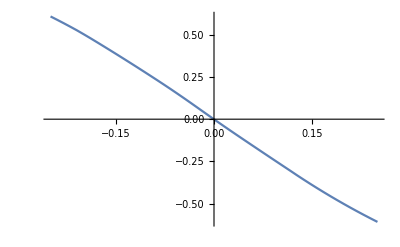

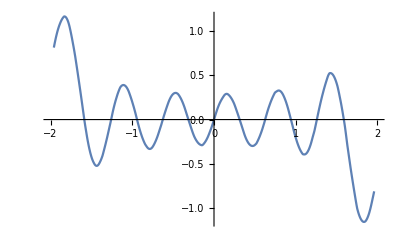

```mathematica
Plot[funs[[13]][0.1,y], {y,-0.25,0.25}]
Plot[funs[[35]][x,0.1], {x,-2,2}]
```

```mathematica
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

```mathematica
k = Table[{1/R[[1]] Length[findAllRoots[funs[[Ordering[Abs[Eigenvectors[Pm.Lm][[i]]],-1][[1]]]][x,0.1],{x,-R[[1]],R[[1]]}]] Pi, Mod[Length[findAllRoots[funs[[Ordering[Abs[Eigenvectors[Pm.Lm][[i]]],-1][[1]]]][0.1,y],{y,-R[[2]],R[[2]]}]],2]},{i,1,n}]
data=Transpose@{k,Sqrt[Eigenvalues[Pm.Lm]]};
```

{{0,1},{(13 π)/2,0},{(13 π)/2,0},{4 π,0},{(3 π)/2,1},{(7 π)/2,0},{6 π,0},{(7 π)/2,0},{(11 π)/2,0},{5 π,1},{(7 π)/2,0},{(9 π)/2,1},{(5 π)/2,0},{5 π,0},{4 π,1},{π,0},{2 π,0},{(7 π)/2,1},{(3 π)/2,0},{(9 π)/2,0},{3 π,1},{(5 π)/2,1},{(7 π)/2,0},{2 π,1},{(3 π)/2,1},{3 π,0},{π,1},{π/2,1},{0,1},{2 π,0},{(3 π)/2,0},{π,0},{π/2,0},{4 π,0},{4 π,0}}

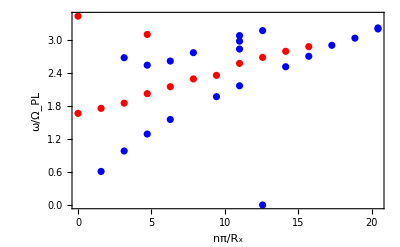

```mathematica
data=Transpose@{k[[;;,1]],Sqrt[Eigenvalues[Pm.Lm]], k[[;;,2]]};
ListPlot[{Transpose@{SplitBy[Sort[data, #1[[3]]==0&], #[[3]]==0&][[1]][[;;,1]], SplitBy[Sort[data, #1[[3]]==0&], #[[3]]==0&][[1]][[;;,2]]}, Transpose@{SplitBy[Sort[data, #1[[3]]==0&], #[[3]]==0&][[2]][[;;,1]], SplitBy[Sort[data, #1[[3]]==0&], #[[3]]==0&][[2]][[;;,2]]}}, AxesLabel->{"nπ/L", "ω/Ω"}, PlotStyle->{Blue, Red}, Frame->True,FrameLabel->{{Style["ω/Ω_PL",Bold,12],""},{Style["nπ/R_x",Bold,12],""}}]
```

```mathematica
findAllRoots[funs[[25]][1,y],{y,-0.25,0.25}]
```

{}

```mathematica
funs[[25]][1,-0.25]
```

-0.145398

```mathematica
Export["CirkelRx2Ry0.5n35LmPm28dec.csv", Lm . Pm, "CSV"]
```

CirkelRx2Ry0.5n35LmPm28dec.csv

```mathematica
Sqrt[Eigenvalues[Pm.Lm]]
```

{3.43665,3.22254,3.20263,3.17316,3.10355,3.08266,3.03554,2.98071,2.90537,2.8813,2.83763,2.79638,2.77149,2.70562,2.68582,2.67964,2.61883,2.57642,2.5441,2.51484,2.3588,2.29393,2.16905,2.15218,2.02525,1.97049,1.85267,1.75786,1.66668,1.55565,1.29028,0.981612,0.609796,0.+0.148202 ⅈ,1.32615×10^-7}

```mathematica
Eigenvectors[Pm.Lm][[6]]
```

{-6.35817×10^-19,-0.00106591,-0.000236993,-0.00354303,-0.00229013,-0.00746609,0.0148882,-0.0926981,-0.0104582,0.00310965,0.00914712,-0.0427084,-0.00470736,-0.0154823,-0.188568,-0.0662166,-0.0197893,-0.0389861,0.0521161,0.046764,-0.00708734,0.0131193,0.0269081,0.00251723,-0.104089,-0.0482148,0.088205,0.716706,-0.448564,-0.0186784,-0.282061,0.0127391,0.297647,-0.00440142,0.191345}

R={2,0.5}
n = 35
t=24897s -> 7uur